```mathematica
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__] :>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:> Sequence[],{var_,1}:> {var}}]]
```

```mathematica
meq=Inactive[DSolve][D[u[t,x,y],x]+D[v[t,x,y],y]==0,{u,v},{t,x,y}]
```

DSolve[v^(0,0,1)[t,x,y]+u^(0,1,0)[t,x,y]==0,{u,v},{t,x,y}]

```mathematica
U=u[t,x,y];
ux=D[U,x];
uy=D[U,y];
uxx=D[U,{x,2}];
uyy=D[U,{y,2}];
ut=D[U,t];

V=v[t,x,y];
vx=D[V,x];
vy=D[V,y];
vxx=D[V,{x,2}];
vyy=D[V,{y,2}];
vt=D[V,t];

P=p[t,x,y];
px=D[P,x];
py=D[P,y];

TT=T[t,x,y];
Tt=D[TT,t];
Tx=D[TT,x];
Ty=D[TT,y];
Txx=D[TT,{x,2}];
Tyy=D[TT,{y,2}];
mu=μ[TT];
dmu=μ'[TT];
unknowns={u,v,p,T};
params={t,x,y};
```

```mathematica
meq=ux+vy==0;
ueq=ρ ut+ρ(U ux + V uy)==-px -ρ g +mu(uxx+uyy)+dmu(2ux Tx+(uy+vx)Ty);
veq=ρ vt+ρ(U vx + V vy)==-py +mu(vxx+vyy)+dmu((uy+vx) Tx+2vy Ty);
Teq=ρ c Tt + ρ c (U Tx+V Ty)==-k(Txx+Tyy)+mu(2 ux^2+2 uy^2+(uy+vx)^2);
equations={meq,ueq,veq,Teq};
Grid[Transpose[{{"Mass balance","Momentum, x","Momentum, y","Energy balance"},equations}],Frame->All,Alignment->Left]//pdConv
```

Mass balance | (∂u(t,x,y))/(∂x)+(∂v(t,x,y))/(∂y)==0
Momentum, x | ρ (v(t,x,y) (∂u(t,x,y))/(∂y)+u(t,x,y) (∂u(t,x,y))/(∂x))+ρ (∂u(t,x,y))/(∂t)==-(∂p(t,x,y))/(∂x)+(∂μ(T(t,x,y)))/(∂T(t,x,y)) ((∂T(t,x,y))/(∂y) ((∂u(t,x,y))/(∂y)+(∂v(t,x,y))/(∂x))+2 (∂T(t,x,y))/(∂x) (∂u(t,x,y))/(∂x))+μ(T(t,x,y)) ((∂^2 u(t,x,y))/(∂x^2)+(∂^2 u(t,x,y))/(∂y^2))-g ρ
Momentum, y | ρ (u(t,x,y) (∂v(t,x,y))/(∂x)+v(t,x,y) (∂v(t,x,y))/(∂y))+ρ (∂v(t,x,y))/(∂t)==-(∂p(t,x,y))/(∂y)+(∂μ(T(t,x,y)))/(∂T(t,x,y)) ((∂T(t,x,y))/(∂x) ((∂u(t,x,y))/(∂y)+(∂v(t,x,y))/(∂x))+2 (∂T(t,x,y))/(∂y) (∂v(t,x,y))/(∂y))+μ(T(t,x,y)) ((∂^2 v(t,x,y))/(∂x^2)+(∂^2 v(t,x,y))/(∂y^2))
Energy balance | c ρ (u(t,x,y) (∂T(t,x,y))/(∂x)+v(t,x,y) (∂T(t,x,y))/(∂y))+c ρ (∂T(t,x,y))/(∂t)==μ(T(t,x,y)) (((∂u(t,x,y))/(∂y)+(∂v(t,x,y))/(∂x))^2+2 ((∂u(t,x,y))/(∂x))^2+2 ((∂u(t,x,y))/(∂y))^2)-k ((∂^2 T(t,x,y))/(∂x^2)+(∂^2 T(t,x,y))/(∂y^2))

```mathematica
newUnknowns=unknowns;
DSolveChangeVariables[Inactive[DSolve][equations,unknowns,params],newUnknowns,{t,x,ξ},{ξ==y/h[t,x]}]
```

DSolve[{-(ξ h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+(v^(0,0,1)[t,x,ξ])/h[t,x]+u^(0,1,0)[t,x,ξ]==0,ρ ((v[t,x,ξ] u^(0,0,1)[t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+u^(0,1,0)[t,x,ξ]))+ρ (-(ξ h^(1,0)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+u^(1,0,0)[t,x,ξ])==-g ρ+(ξ h^(0,1)[t,x] p^(0,0,1)[t,x,ξ])/h[t,x]-p^(0,1,0)[t,x,ξ]+μ'[T[t,x,ξ]] (2 (-(ξ h^(0,1)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(0,1,0)[t,x,ξ]) (-(ξ h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+u^(0,1,0)[t,x,ξ])+(T^(0,0,1)[t,x,ξ] ((u^(0,0,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]+v^(0,1,0)[t,x,ξ]))/h[t,x])+μ[T[t,x,ξ]] ((ξ (h^(0,1)[t,x])^2 u^(0,0,1)[t,x,ξ])/h[t,x]^2-(ξ h^(0,2)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+(u^(0,0,2)[t,x,ξ])/h[t,x]^2-(ξ h^(0,1)[t,x] u^(0,1,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] (-(h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] u^(0,0,2)[t,x,ξ])/h[t,x]+u^(0,1,1)[t,x,ξ]))/h[t,x]+u^(0,2,0)[t,x,ξ]),ρ ((v[t,x,ξ] v^(0,0,1)[t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ h^(0,1)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]+v^(0,1,0)[t,x,ξ]))+ρ (-(ξ h^(1,0)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]+v^(1,0,0)[t,x,ξ])==-(p^(0,0,1)[t,x,ξ])/h[t,x]+μ'[T[t,x,ξ]] ((2 T^(0,0,1)[t,x,ξ] v^(0,0,1)[t,x,ξ])/h[t,x]^2+(-(ξ h^(0,1)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(0,1,0)[t,x,ξ]) ((u^(0,0,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]+v^(0,1,0)[t,x,ξ]))+μ[T[t,x,ξ]] ((ξ (h^(0,1)[t,x])^2 v^(0,0,1)[t,x,ξ])/h[t,x]^2-(ξ h^(0,2)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]+(v^(0,0,2)[t,x,ξ])/h[t,x]^2-(ξ h^(0,1)[t,x] v^(0,1,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] (-(h^(0,1)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] v^(0,0,2)[t,x,ξ])/h[t,x]+v^(0,1,1)[t,x,ξ]))/h[t,x]+v^(0,2,0)[t,x,ξ]),c ρ ((v[t,x,ξ] T^(0,0,1)[t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ h^(0,1)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(0,1,0)[t,x,ξ]))+c ρ (-(ξ h^(1,0)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(1,0,0)[t,x,ξ])==μ[T[t,x,ξ]] ((2 (u^(0,0,1)[t,x,ξ])^2)/h[t,x]^2+2 (-(ξ h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+u^(0,1,0)[t,x,ξ])^2+((u^(0,0,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] v^(0,0,1)[t,x,ξ])/h[t,x]+v^(0,1,0)[t,x,ξ])^2)-k ((ξ (h^(0,1)[t,x])^2 T^(0,0,1)[t,x,ξ])/h[t,x]^2-(ξ h^(0,2)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+(T^(0,0,2)[t,x,ξ])/h[t,x]^2-(ξ h^(0,1)[t,x] T^(0,1,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] (-(h^(0,1)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]-(ξ h^(0,1)[t,x] T^(0,0,2)[t,x,ξ])/h[t,x]+T^(0,1,1)[t,x,ξ]))/h[t,x]+T^(0,2,0)[t,x,ξ])},{u,v,p,T},{t,x,ξ}]

```mathematica
teqs={-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+(Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[0,1,0][u][t,x,ξ]==0,ρ ((v[t,x,ξ] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+Derivative[0,1,0][u][t,x,ξ]))+ρ (-(ξ Derivative[1,0][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+Derivative[1,0,0][u][t,x,ξ])==-g ρ+(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][p][t,x,ξ])/h[t,x]-Derivative[0,1,0][p][t,x,ξ]+μ'[T[t,x,ξ]] (2 (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[0,1,0][T][t,x,ξ]) (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+Derivative[0,1,0][u][t,x,ξ])+(Derivative[0,0,1][T][t,x,ξ] ((Derivative[0,0,1][u][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[0,1,0][v][t,x,ξ]))/h[t,x])+μ[T[t,x,ξ]] ((ξ (Derivative[0,1][h][t,x])^2 Derivative[0,0,1][u][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,2][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+(Derivative[0,0,2][u][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,1][h][t,x] Derivative[0,1,1][u][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] (-(Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] Derivative[0,0,2][u][t,x,ξ])/h[t,x]+Derivative[0,1,1][u][t,x,ξ]))/h[t,x]+Derivative[0,2,0][u][t,x,ξ]),ρ ((v[t,x,ξ] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[0,1,0][v][t,x,ξ]))+ρ (-(ξ Derivative[1,0][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[1,0,0][v][t,x,ξ])==-(Derivative[0,0,1][p][t,x,ξ])/h[t,x]+μ'[T[t,x,ξ]] ((2 Derivative[0,0,1][T][t,x,ξ] Derivative[0,0,1][v][t,x,ξ])/h[t,x]^2+(-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[0,1,0][T][t,x,ξ]) ((Derivative[0,0,1][u][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[0,1,0][v][t,x,ξ]))+μ[T[t,x,ξ]] ((ξ (Derivative[0,1][h][t,x])^2 Derivative[0,0,1][v][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,2][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+(Derivative[0,0,2][v][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,1][h][t,x] Derivative[0,1,1][v][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] (-(Derivative[0,1][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] Derivative[0,0,2][v][t,x,ξ])/h[t,x]+Derivative[0,1,1][v][t,x,ξ]))/h[t,x]+Derivative[0,2,0][v][t,x,ξ]),c ρ ((v[t,x,ξ] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[0,1,0][T][t,x,ξ]))+c ρ (-(ξ Derivative[1,0][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[1,0,0][T][t,x,ξ])==μ[T[t,x,ξ]] ((2 (Derivative[0,0,1][u][t,x,ξ])^2)/h[t,x]^2+2 (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+Derivative[0,1,0][u][t,x,ξ])^2+((Derivative[0,0,1][u][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[0,1,0][v][t,x,ξ])^2)-k ((ξ (Derivative[0,1][h][t,x])^2 Derivative[0,0,1][T][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,2][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+(Derivative[0,0,2][T][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,1][h][t,x] Derivative[0,1,1][T][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] (-(Derivative[0,1][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]-(ξ Derivative[0,1][h][t,x] Derivative[0,0,2][T][t,x,ξ])/h[t,x]+Derivative[0,1,1][T][t,x,ξ]))/h[t,x]+Derivative[0,2,0][T][t,x,ξ])};
```

```mathematica
teqss=Simplify[teqs];
```

```mathematica
Grid[Transpose[{{"Mass balance","Momentum, x","Momentum, y","Energy balance"},teqs}],Frame->All,Alignment->Left]//pdConv
```

Mass balance | -(ξ (∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))+((∂v(t,x,ξ))/(∂ξ))/(h(t,x))+(∂u(t,x,ξ))/(∂x)==0
Momentum, x | ρ ((v(t,x,ξ) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))+u(t,x,ξ) ((∂u(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))))+ρ ((∂u(t,x,ξ))/(∂t)-(ξ (∂h(t,x))/(∂t) (∂u(t,x,ξ))/(∂ξ))/(h(t,x)))==μ(T(t,x,ξ)) (-(ξ (∂h(t,x))/(∂x) ((∂^2 u(t,x,ξ))/(∂x ∂ξ)-(ξ (∂h(t,x))/(∂x) (∂^2 u(t,x,ξ))/(∂ξ^2))/(h(t,x))-((∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂^2 u(t,x,ξ))/(∂x ∂ξ))/(h(t,x))-(ξ (∂^2 h(t,x))/(∂x^2) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))+((∂^2 u(t,x,ξ))/(∂ξ^2))/(h(t,x))^2+(ξ ((∂h(t,x))/(∂x))^2 (∂u(t,x,ξ))/(∂ξ))/(h(t,x))^2+(∂^2 u(t,x,ξ))/(∂x^2))+(ξ (∂h(t,x))/(∂x) (∂p(t,x,ξ))/(∂ξ))/(h(t,x))+(∂μ(T(t,x,ξ)))/(∂T(t,x,ξ)) (((∂T(t,x,ξ))/(∂ξ) (((∂u(t,x,ξ))/(∂ξ))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂v(t,x,ξ))/(∂ξ))/(h(t,x))+(∂v(t,x,ξ))/(∂x)))/(h(t,x))+2 ((∂T(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂T(t,x,ξ))/(∂ξ))/(h(t,x))) ((∂u(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))))-(∂p(t,x,ξ))/(∂x)-g ρ
Momentum, y | ρ (u(t,x,ξ) ((∂v(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂v(t,x,ξ))/(∂ξ))/(h(t,x)))+(v(t,x,ξ) (∂v(t,x,ξ))/(∂ξ))/(h(t,x)))+ρ ((∂v(t,x,ξ))/(∂t)-(ξ (∂h(t,x))/(∂t) (∂v(t,x,ξ))/(∂ξ))/(h(t,x)))==μ(T(t,x,ξ)) (-(ξ (∂h(t,x))/(∂x) ((∂^2 v(t,x,ξ))/(∂x ∂ξ)-(ξ (∂h(t,x))/(∂x) (∂^2 v(t,x,ξ))/(∂ξ^2))/(h(t,x))-((∂h(t,x))/(∂x) (∂v(t,x,ξ))/(∂ξ))/(h(t,x))))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂^2 v(t,x,ξ))/(∂x ∂ξ))/(h(t,x))-(ξ (∂^2 h(t,x))/(∂x^2) (∂v(t,x,ξ))/(∂ξ))/(h(t,x))+((∂^2 v(t,x,ξ))/(∂ξ^2))/(h(t,x))^2+(ξ ((∂h(t,x))/(∂x))^2 (∂v(t,x,ξ))/(∂ξ))/(h(t,x))^2+(∂^2 v(t,x,ξ))/(∂x^2))-((∂p(t,x,ξ))/(∂ξ))/(h(t,x))+(∂μ(T(t,x,ξ)))/(∂T(t,x,ξ)) (((∂T(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂T(t,x,ξ))/(∂ξ))/(h(t,x))) (((∂u(t,x,ξ))/(∂ξ))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂v(t,x,ξ))/(∂ξ))/(h(t,x))+(∂v(t,x,ξ))/(∂x))+(2 (∂T(t,x,ξ))/(∂ξ) (∂v(t,x,ξ))/(∂ξ))/(h(t,x))^2)
Energy balance | c ρ (u(t,x,ξ) ((∂T(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂T(t,x,ξ))/(∂ξ))/(h(t,x)))+(v(t,x,ξ) (∂T(t,x,ξ))/(∂ξ))/(h(t,x)))+c ρ ((∂T(t,x,ξ))/(∂t)-(ξ (∂h(t,x))/(∂t) (∂T(t,x,ξ))/(∂ξ))/(h(t,x)))==μ(T(t,x,ξ)) ((((∂u(t,x,ξ))/(∂ξ))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂v(t,x,ξ))/(∂ξ))/(h(t,x))+(∂v(t,x,ξ))/(∂x))^2+(2 ((∂u(t,x,ξ))/(∂ξ))^2)/(h(t,x))^2+2 ((∂u(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x)))^2)-k (-(ξ (∂h(t,x))/(∂x) ((∂^2 T(t,x,ξ))/(∂x ∂ξ)-(ξ (∂h(t,x))/(∂x) (∂^2 T(t,x,ξ))/(∂ξ^2))/(h(t,x))-((∂h(t,x))/(∂x) (∂T(t,x,ξ))/(∂ξ))/(h(t,x))))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂^2 T(t,x,ξ))/(∂x ∂ξ))/(h(t,x))-(ξ (∂^2 h(t,x))/(∂x^2) (∂T(t,x,ξ))/(∂ξ))/(h(t,x))+((∂^2 T(t,x,ξ))/(∂ξ^2))/(h(t,x))^2+(ξ ((∂h(t,x))/(∂x))^2 (∂T(t,x,ξ))/(∂ξ))/(h(t,x))^2+(∂^2 T(t,x,ξ))/(∂x^2))

```mathematica
meq=ux+vy==0;
ueq=0==-px -ρ g +D[mu uy,y];
veq=0==-py +D[mu uy,x]+D[2mu vy,y];
Teq=ρ c Tt + ρ c (U Tx+V Ty)==-k Tyy+mu uy^2;
equations={meq,ueq,veq,Teq};
Grid[Transpose[{{"Mass balance","Momentum, x","Momentum, y","Energy balance"},equations}],Frame->All,Alignment->Left]//pdConv
```

Mass balance | (∂u(t,x,y))/(∂x)+(∂v(t,x,y))/(∂y)==0
Momentum, x | 0==-(∂p(t,x,y))/(∂x)+μ(T(t,x,y)) (∂^2 u(t,x,y))/(∂y^2)+(∂T(t,x,y))/(∂y) (∂u(t,x,y))/(∂y) (∂μ(T(t,x,y)))/(∂T(t,x,y))-g ρ
Momentum, y | 0==μ(T(t,x,y)) (∂^2 u(t,x,y))/(∂x ∂y)-(∂p(t,x,y))/(∂y)+(∂T(t,x,y))/(∂x) (∂u(t,x,y))/(∂y) (∂μ(T(t,x,y)))/(∂T(t,x,y))+2 μ(T(t,x,y)) (∂^2 v(t,x,y))/(∂y^2)+2 (∂T(t,x,y))/(∂y) (∂v(t,x,y))/(∂y) (∂μ(T(t,x,y)))/(∂T(t,x,y))
Energy balance | c ρ (u(t,x,y) (∂T(t,x,y))/(∂x)+v(t,x,y) (∂T(t,x,y))/(∂y))+c ρ (∂T(t,x,y))/(∂t)==μ(T(t,x,y)) ((∂u(t,x,y))/(∂y))^2-k (∂^2 T(t,x,y))/(∂y^2)

```mathematica
newUnknowns=unknowns;
DSolveChangeVariables[Inactive[DSolve][equations,unknowns,params],newUnknowns,{t,x,ξ},{ξ==y/h[t,x]}]
```

DSolve[{-(ξ h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]+(v^(0,0,1)[t,x,ξ])/h[t,x]+u^(0,1,0)[t,x,ξ]==0,0==-g ρ+(ξ h^(0,1)[t,x] p^(0,0,1)[t,x,ξ])/h[t,x]+(μ'[T[t,x,ξ]] T^(0,0,1)[t,x,ξ] u^(0,0,1)[t,x,ξ])/h[t,x]^2+(μ[T[t,x,ξ]] u^(0,0,2)[t,x,ξ])/h[t,x]^2-p^(0,1,0)[t,x,ξ],0==-(p^(0,0,1)[t,x,ξ])/h[t,x]+(2 μ'[T[t,x,ξ]] T^(0,0,1)[t,x,ξ] v^(0,0,1)[t,x,ξ])/h[t,x]^2+(2 μ[T[t,x,ξ]] v^(0,0,2)[t,x,ξ])/h[t,x]^2+(μ'[T[t,x,ξ]] u^(0,0,1)[t,x,ξ] (-(ξ h^(0,1)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(0,1,0)[t,x,ξ]))/h[t,x]+μ[T[t,x,ξ]] (-(h^(0,1)[t,x] u^(0,0,1)[t,x,ξ])/h[t,x]^2-(ξ h^(0,1)[t,x] u^(0,0,2)[t,x,ξ])/h[t,x]^2+(u^(0,1,1)[t,x,ξ])/h[t,x]),c ρ ((v[t,x,ξ] T^(0,0,1)[t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ h^(0,1)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(0,1,0)[t,x,ξ]))+c ρ (-(ξ h^(1,0)[t,x] T^(0,0,1)[t,x,ξ])/h[t,x]+T^(1,0,0)[t,x,ξ])==(μ[T[t,x,ξ]] (u^(0,0,1)[t,x,ξ])^2)/h[t,x]^2-(k T^(0,0,2)[t,x,ξ])/h[t,x]^2},{u,v,p,T},{t,x,ξ}]

```mathematica
teqs={-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]+(Derivative[0,0,1][v][t,x,ξ])/h[t,x]+Derivative[0,1,0][u][t,x,ξ]==0,0==-g ρ+(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][p][t,x,ξ])/h[t,x]+(μ'[T[t,x,ξ]] Derivative[0,0,1][T][t,x,ξ] Derivative[0,0,1][u][t,x,ξ])/h[t,x]^2+(μ[T[t,x,ξ]] Derivative[0,0,2][u][t,x,ξ])/h[t,x]^2-Derivative[0,1,0][p][t,x,ξ],0==-(Derivative[0,0,1][p][t,x,ξ])/h[t,x]+(2 μ'[T[t,x,ξ]] Derivative[0,0,1][T][t,x,ξ] Derivative[0,0,1][v][t,x,ξ])/h[t,x]^2+(2 μ[T[t,x,ξ]] Derivative[0,0,2][v][t,x,ξ])/h[t,x]^2+1/h[t,x] μ'[T[t,x,ξ]] Derivative[0,0,1][u][t,x,ξ] (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[0,1,0][T][t,x,ξ])+μ[T[t,x,ξ]] (-(Derivative[0,1][h][t,x] Derivative[0,0,1][u][t,x,ξ])/h[t,x]^2-(ξ Derivative[0,1][h][t,x] Derivative[0,0,2][u][t,x,ξ])/h[t,x]^2+(Derivative[0,1,1][u][t,x,ξ])/h[t,x]),c ρ ((v[t,x,ξ] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+u[t,x,ξ] (-(ξ Derivative[0,1][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[0,1,0][T][t,x,ξ]))+c ρ (-(ξ Derivative[1,0][h][t,x] Derivative[0,0,1][T][t,x,ξ])/h[t,x]+Derivative[1,0,0][T][t,x,ξ])==(μ[T[t,x,ξ]] (Derivative[0,0,1][u][t,x,ξ])^2)/h[t,x]^2-(k Derivative[0,0,2][T][t,x,ξ])/h[t,x]^2};
Grid[Transpose[{{"Mass balance","Momentum, x","Momentum, y","Energy balance"},teqs}],Frame->All,Alignment->Left]//pdConv
```

Mass balance | -(ξ (∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))+((∂v(t,x,ξ))/(∂ξ))/(h(t,x))+(∂u(t,x,ξ))/(∂x)==0
Momentum, x | 0==(ξ (∂h(t,x))/(∂x) (∂p(t,x,ξ))/(∂ξ))/(h(t,x))+(μ(T(t,x,ξ)) (∂^2 u(t,x,ξ))/(∂ξ^2))/(h(t,x))^2+((∂T(t,x,ξ))/(∂ξ) (∂u(t,x,ξ))/(∂ξ) (∂μ(T(t,x,ξ)))/(∂T(t,x,ξ)))/(h(t,x))^2-(∂p(t,x,ξ))/(∂x)-g ρ
Momentum, y | 0==μ(T(t,x,ξ)) (((∂^2 u(t,x,ξ))/(∂x ∂ξ))/(h(t,x))-(ξ (∂h(t,x))/(∂x) (∂^2 u(t,x,ξ))/(∂ξ^2))/(h(t,x))^2-((∂h(t,x))/(∂x) (∂u(t,x,ξ))/(∂ξ))/(h(t,x))^2)-((∂p(t,x,ξ))/(∂ξ))/(h(t,x))+((∂u(t,x,ξ))/(∂ξ) ((∂T(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂T(t,x,ξ))/(∂ξ))/(h(t,x))) (∂μ(T(t,x,ξ)))/(∂T(t,x,ξ)))/(h(t,x))+(2 μ(T(t,x,ξ)) (∂^2 v(t,x,ξ))/(∂ξ^2))/(h(t,x))^2+(2 (∂T(t,x,ξ))/(∂ξ) (∂v(t,x,ξ))/(∂ξ) (∂μ(T(t,x,ξ)))/(∂T(t,x,ξ)))/(h(t,x))^2
Energy balance | c ρ (u(t,x,ξ) ((∂T(t,x,ξ))/(∂x)-(ξ (∂h(t,x))/(∂x) (∂T(t,x,ξ))/(∂ξ))/(h(t,x)))+(v(t,x,ξ) (∂T(t,x,ξ))/(∂ξ))/(h(t,x)))+c ρ ((∂T(t,x,ξ))/(∂t)-(ξ (∂h(t,x))/(∂t) (∂T(t,x,ξ))/(∂ξ))/(h(t,x)))==(μ(T(t,x,ξ)) ((∂u(t,x,ξ))/(∂ξ))^2)/(h(t,x))^2-(k (∂^2 T(t,x,ξ))/(∂ξ^2))/(h(t,x))^2

1.

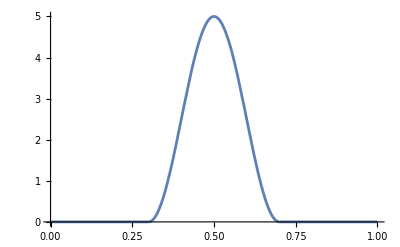

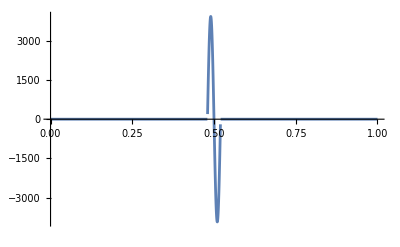

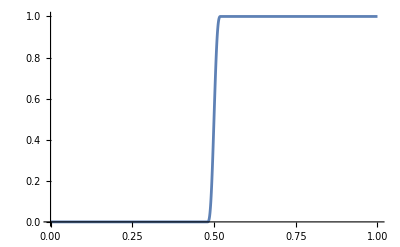

```mathematica
dsmooth[x_,x0_,dx_]:=If[Abs[x-x0]<2 dx,1/(4 dx)(1+Cos[(π(x-x0))/(2 dx)]),0];
dds[x_,x0_,dx_]:=D[dsmooth[x,x0,dx],x];
intds[x_,x0_,dx_]:=Integrate[dsmooth[ξ,x0,dx],{ξ,0,x}];
Integrate[dsmooth[x,0.5,0.1],{x,0,1}]
Plot[dsmooth[x,0.5,0.1],{x,0,1}]
Plot[Evaluate[dds[x,0.5,0.01]],{x,0,1}]
Plot[Evaluate[intds[x,0.5,0.01]],{x,0,1}]
Plot[Evaluate[intds[x,0.5,0.01]],{x,0,1}]
```

```mathematica
Integrate[dsmooth[x,0.5,0.00001],x]
```

Piecewise[{{25000. x+0.159155 Sin[78539.8 (-1.+2. x)], Abs[-0.5+x]<0.00002}, {0., True}}]

```mathematica
D
```

D

```mathematica
dds[0,1,1]
```

D::ivar: 0 is not a valid variable.

∂_0 1/4

```mathematica
ClearAll[x,dx,x0,dsmooth,dds]
```

```mathematica
dds[x,dx,x0]
```

If[Abs[-dx+x]<2 x0,(1+Cos[(π (x-dx))/(2 x0)])/(4 x0),0]^(1,0,0)

```mathematica
Evaluate[dds[x,0.5,0.2]]
```

If[Abs[x-x0]<2 dx,-(π Sin[(π (x-x0))/(2 dx)])/((4 dx) (2 dx)),0][x,0.5,0.2]

```mathematica
Integrate[dsmooth[x,x0,dx],x]
```

Piecewise[{{((x-x0)/2+(dx Sin[(π (x-x0))/(2 dx)])/π)/(2 dx), 2 dx-Abs[x-x0]>0}, {0, True}}]